```mathematica
Clear["Global`*"];
m=1.5;
τ=3×10^-3;
CC=12;
Kp=1000000;
Kτ=10000000000000;
result=NDSolve[{m q''[t]+CC Sign[q'[t]]==-Kp q[t]-Kτ q'[t],q[0]==-5,q'[0]==0},q[t],{t,0,10}]
```

{{q[t]→InterpolatingFunction[…][t]}}

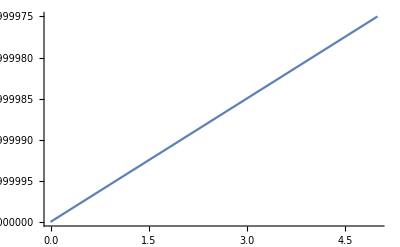

```mathematica
Plot[Evaluate[q[t]/.result],{t,0,5},PlotRange->All]
```